# Liver slices MFA

```mathematica
<<NilssonLab`MetabolicNetwork`
<<NilssonLab`ExtremePathways`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
<<NilssonLab`Visualization`
```

```mathematica
<<NilssonLab`OpenFLUX`
```

```mathematica
<<NilssonLab`IsotopeDistributions`
```

```mathematica
<<NilssonLab`GAMSFluxEstimation`
```

```mathematica
OpenDBConnection[]
```

## Set paths

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\code\liver-flux-analysis\flux-analysis-liver

```mathematica
patientId="L002";
```

```mathematica
experimentId="Human_liver_"<>patientId
```

Human_liver_L002

```mathematica
modelDir="C:\\code\\liver-flux-models\\Models\\liverModel_2_openFluxExport";
```

```mathematica
modelId="liver-model-working"
```

liver-model-working

```mathematica
lcmsDataDir="C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\lcms-data";
```

## Import model

### Import from OpenFLUX format

We only keep the network model from OpenFLUX. (Targets are set from data)

```mathematica
<<NilssonLab`OpenFLUX`
```

```mathematica
{net,atomMaps,targets}=OpenFLUXImport[FileNameJoin[{modelDir,"liver-model_openflux.txt"}]];
```

```mathematica
bnet=BoundaryNetwork[net]
```

<BoundaryNetwork, 33 boundary fluxes>

```mathematica
TableForm[Table[{ReactionID[r],ReactionFormula[net,r]},{r,Reactions[net]}],TableHeadings->{Automatic,None}]
```

1 | 2AMACHYD | 2amac_c + h2o_c ==> nh4_c + pyr_c
2 | ACITL | atp_c + cit_c + coa_c ==> accoa_c + adp_c + oaa_c + pi_c
3 | ACOAHi | accoa_c + h2o_c ==> ac_c + coa_c + h_c
4 | ACONTm | cit_m <=> icit_m
5 | ACRNtm | acrn_c ==> acrn_m
6 | ACS | ac_c + atp_c + coa_c ==> accoa_c + amp_c + ppi_c
7 | ADK1 | amp_c + atp_c ==> 2 adp_c
8 | AKGDm | akg_m + coa_m + nad_m <=> co2_m + nadh_m + succoa_m
9 | AKGtm | akg_c <=> akg_m
10 | ALATA_L | akg_c + ala-L_c <=> glu-L_c + pyr_c
11 | ARGN | arg-L_c + h2o_c ==> orn_c + urea_c
12 | ARGSL | argsuc_c ==> arg-L_c + fum_c
13 | ARGSS | asp-L_c + atp_c + citr-L_c ==> amp_c + argsuc_c + h_c + ppi_c
14 | ASPTA | akg_c + asp-L_c <=> glu-L_c + oaa_c
15 | ASPTAm | glu-L_m + oaa_m <=> akg_m + asp-L_m
16 | ASPtm | asp-L_m ==> asp-L_c
17 | ATPS4m | adp_m + 4 h_ims_m + pi_m ==> atp_m + h2o_m + 3 h_m
18 | ATPtm | adp_c + atp_m <=> adp_m + atp_c
19 | CBPSam | 2 atp_m + hco3_m + nh4_m ==> 2 adp_m + cbp_m + 2 h_m + pi_m
20 | CELLWORK | atp_c + h2o_c ==> adp_c + energy_c + h_c + pi_c
21 | CITtm | cit_m ==> cit_c
22 | CO2tm | co2_c <=> co2_m
23 | CRNtim | crn_m ==> crn_c
24 | CSm | accoa_m + h2o_m + oaa_m ==> cit_m + coa_m + h_m
25 | CSNATm | acrn_m + coa_m ==> accoa_m + crn_m
26 | CSNATr | accoa_c + crn_c ==> acrn_c + coa_c
27 | CYOOm | 4 focytC_m + 8 h_m + o2_m ==> 4 ficytC_m + 2 h2o_m + 4 h_ims_m
28 | CYOR-u10m | 2 ficytC_m + 2 h_m + q10h2_m ==> 2 focytC_m + 4 h_ims_m + q10_m
29 | ENO | 2pg_c <=> h2o_c + pep_c
30 | FBA | fdp_c <=> dhap_c + g3p_c
31 | FBP | fdp_c + h2o_c ==> f6p_c + pi_c
32 | FUMm | fum_m + h2o_m ==> mal-L_m
33 | FUMtm | fum_c ==> fum_m
34 | G3PD1 | dhap_c + h_c + nadh_c ==> glyc3p_c + nad_c
35 | G6PPer | g6p_r + h2o_r ==> glc-D_r + pi_r
36 | G6Pter | g6p_r ==> g6p_c
37 | GAPD | g3p_c + nad_c + pi_c <=> 13dpg_c + h_c + nadh_c
38 | GHMT2r | ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c
39 | GLCmix | glc-D_v ==> glc-D_e
40 | GLCtin | glc-D_v ==> glc-D_c
41 | GLCtout | glc-D_r ==> glc-D_e
42 | GLNtm | gln-L_c ==> gln-L_m
43 | GLUDxm | glu-L_m + h2o_m + nad_m <=> akg_m + h_m + nadh_m + nh4_m
44 | GLUNm | gln-L_m + h2o_m <=> glu-L_m + nh4_m
45 | GLUt2m | glu-L_c <=> glu-L_m
46 | GLYCOGEN_BREAK | glycogen_r + pi_c ==> g1p_r
47 | GLYCPH | glyc3p_c + h2o_c ==> glyc_c + pi_c
48 | GLYK | atp_c + glyc_c ==> adp_c + glyc3p_c + h_c
49 | GTHS | atp_c + glucys_c + gly_c ==> adp_c + gthrd_c + h_c + pi_c
50 | H2Oter | h2o_c ==> h2o_r
51 | H2Otm | h2o_c <=> h2o_m
52 | HCO3Em | co2_m + h2o_m ==> hco3_m + h_m
53 | HEX1 | atp_c + glc-D_c ==> adp_c + g6p_c + h_c
54 | Htm2 | h_m <=> h_c
55 | ICDHxm | icit_m + nad_m <=> akg_m + co2_m + nadh_m
56 | LDH_L | h_c + nadh_c + pyr_c <=> lac-L_c + nad_c
57 | MALtm | mal-L_c ==> mal-L_m
58 | MDH | h_c + nadh_c + oaa_c ==> mal-L_c + nad_c
59 | MDHm | mal-L_m + nad_m <=> h_m + nadh_m + oaa_m
60 | NADH2-u10m | 5 h_m + nadh_m + q10_m ==> 4 h_ims_m + nad_m + q10h2_m
61 | NADH_REDOX | nadh_c <=> h_c + nad_c
62 | NDPK1 | atp_c + gdp_c ==> adp_c + gtp_c
63 | NH4tm | nh4_c <=> nh4_m
64 | O2tm | o2_c ==> o2_m
65 | OCBTm | cbp_m + orn_m ==> citr-L_m + h_m + pi_m
66 | ORNt4m | citr-L_m + orn_c ==> citr-L_c + orn_m
67 | PCm | atp_m + hco3_m + pyr_m ==> adp_m + h_m + oaa_m + pi_m
68 | PDHm | coa_m + nad_m + pyr_m ==> accoa_m + co2_m + nadh_m
69 | PEPCK | gtp_c + oaa_c ==> co2_c + gdp_c + pep_c
70 | PFK | atp_c + f6p_c ==> adp_c + fdp_c + h_c
71 | PGCD | 3pg_c + nad_c ==> 3php_c + h_c + nadh_c
72 | PGI | g6p_c <=> f6p_c
73 | PGK | 13dpg_c + adp_c <=> 3pg_c + atp_c
74 | PGM | 3pg_c <=> 2pg_c
75 | PGMTer | g1p_r ==> g6p_r
76 | PIt2m | pi_c ==> pi_m
77 | PIter | pi_r ==> pi_c
78 | PPA | h2o_c + ppi_c ==> h_c + 2 pi_c
79 | PROTDEG_ALA | prot_ala_c ==> ala-L_c
80 | PROTDEG_ARG | prot_arg_l ==> arg-L_l
81 | PSERT | 3php_c + glu-L_c ==> akg_c + pser-L_c
82 | PSP_L | h2o_c + pser-L_c ==> pi_c + ser-L_c
83 | PYK | adp_c + h_c + pep_c ==> atp_c + pyr_c
84 | PYRt2m | pyr_c <=> pyr_m
85 | SERHL | ser-L_c ==> 2amac_c + h2o_c
86 | SUCD1m | q10_m + succ_m ==> fum_m + q10h2_m
87 | SUCOASm | adp_m + pi_m + succoa_m ==> atp_m + coa_m + succ_m
88 | TPI | dhap_c <=> g3p_c
89 | ARG_tmL | arg-L_l ==> arg-L_c

```mathematica
BoundaryFluxNames[bnet]
```

{ac_IN,ala-L_IN,arg-L_IN,asp-L_IN,co2_IN,glc-D_IN,gln-L_IN,glucys_IN,gly_IN,glyc_IN,glycogen_IN,h2o_IN,h_IN,nh4_IN,o2_IN,prot_ala_IN,prot_arg_IN,ser-L_IN,ala-L_OUT,arg-L_OUT,asp-L_OUT,co2_OUT,energy_OUT,glc-D_OUT,glu-L_OUT,glyc_OUT,gthrd_OUT,h2o_OUT,h_OUT,lac-L_OUT,nh4_OUT,ser-L_OUT,urea_OUT}

### Substrate distributions

List the input metabolites that have atom information; for these the isotope distributions must be specified.

```mathematica
substrateDist=ImportMixtureID[FileNameJoin[{modelDir,"substrate-distributions.txt"}]]
```

{2mop_i→NaturalIsotopomerDistribution[{4},{0.99}],ac_i→NaturalIsotopomerDistribution[{2},{0.0107}],ala-L_i→NaturalIsotopomerDistribution[{3},{0.99}],arg-L_i→NaturalIsotopomerDistribution[{6},{0.99}],asp-L_i→NaturalIsotopomerDistribution[{4},{0.99}],co2_i→NaturalIsotopomerDistribution[{1},{0.0107}],glc-D_i→NaturalIsotopomerDistribution[{6},{0.99}],gln-L_i→NaturalIsotopomerDistribution[{5},{0.99}],glucys_i→NaturalIsotopomerDistribution[{8},{0.0107}],gly_i→NaturalIsotopomerDistribution[{2},{0.99}],glyc_i→NaturalIsotopomerDistribution[{3},{0.0107}],glycogen_i→NaturalIsotopomerDistribution[{6},{0.0107}],prot_ala_i→NaturalIsotopomerDistribution[{3},{0.0107}],prot_arg_i→NaturalIsotopomerDistribution[{6},{0.0107}],ser-L_i→NaturalIsotopomerDistribution[{3},{0.99}]}

### Check atom map

Consistency check. Missing data for cofactors is okay at this stage as long as they are removed below.

```mathematica
CheckAtomMap[atomMaps]
```

{}

Create boundary atom maps (only needed for uptake reactions!)

```mathematica
bmaps=BoundaryAtomMaps[net,atomMaps];
bmaps//Length
```

33

### Symmetry

Note: this will not account for any symmeric metabolites in model that are absent from the database

```mathematica
symmetry=GetSymmetryMap[atomMaps]
```

{fum→{{1,2},{3,4}},succ→{{1,2},{3,4}}}

## Import LCMS data

### From peak area data

Import peak areas. We do not normalize at this step since peak areas are needed for uptake/release measurements

```mathematica
{measuredMetIds,sampleIds,measuredMIDs}=ImportMIDTable[FileNameJoin[{lcmsDataDir,"L002",experimentId<>".tsv"}]];
```

Drop any measured metabolites not in the model

```mathematica
Complement[Flatten[measuredMetIds],MetaboliteID/@Metabolite/@targets]
```

{acrn,ahcys,asn-L,creat,crn,dhdascb,fru,g3pc,gchola,glcnt,glcur,gthrd,gudac,his-L,ile-L,imp,inost,Lcystin,leu-L,lys-L,met-L,nad,nadh,phe-L,pmtcrn,pro-L,r5p,sbt-D,thr-L,trp-L,tyr-L,udpg,ump,urate,val-L}

```mathematica
Block[{ix},
ix=DeleteDuplicates[
First/@Position[measuredMetIds,Alternatives@@(MetaboliteID/@Metabolite/@targets)]];
measuredMIDs=measuredMIDs⟦ix⟧;
measuredMetIds=measuredMetIds⟦ix⟧;]
```

```mathematica
Length[measuredMetIds]
```

14

### Sample annotations

Import as a rule table

```mathematica
sampleInfo=Import[
FileNameJoin[{lcmsDataDir,patientId,experimentId<>"_sampleinfo.tsv"}]];
sampleInfoFactors=Rest[First[sampleInfo]];
sampleInfo=Rest[sampleInfo ];
```

```mathematica
sampleInfo=Replace[sampleIds,Map[Rule[First[#],Rest[#]]&,sampleInfo],{1}]
```

{{tissue slice 0h,tissue extract,,L002,,human},{tissue slice 0h,tissue extract,,L002,,human},{tissue slice 0h,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,13C,L002,,human},{tissue slice 24h,tissue extract,13C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 24h,medium,13C,L002,,human},{spent medium 24h,medium,13C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{fresh medium 0h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 0h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{,plasma,,L002,,human}}

### Targets and mixing matrix

Mapping of measured (simulated) intracellular and extracellular metabolites to targets

```mathematica
measuredMap=Replace[targets,
{EMU[Metabolite[m_,Except["Extracellular"],_],_]:>{First[Cases[measuredMetIds,ml_/;MemberQ[ml,m]]],"tissue slice 24h"},
EMU[Metabolite[m_,"Extracellular",_],_]:>{First[Cases[measuredMetIds,ml_/;MemberQ[ml,m]]],"spent medium 24h"}},{1}];
```

```mathematica
TableForm[measuredMap,TableHeadings->{targets,None}]
```

<akg_m{(12345)}> | akg | tissue slice 24h
<akg_c{(12345)}> | akg | tissue slice 24h
<ala-L_c{(123)}> | ala-L | tissue slice 24h
<arg-L_c{(123456)}> | arg-L | tissue slice 24h
<arg-L_l{(123456)}> | arg-L | tissue slice 24h
<asp-L_c{(1234)}> | asp-L | tissue slice 24h
<asp-L_m{(1234)}> | asp-L | tissue slice 24h
<citr-L_c{(123456)}> | citr-L | tissue slice 24h
<citr-L_m{(123456)}> | citr-L | tissue slice 24h
<f6p_c{(123456)}> | f6p
g1p
g6p | tissue slice 24h
<g1p_r{(123456)}> | f6p
g1p
g6p | tissue slice 24h
<g6p_c{(123456)}> | f6p
g1p
g6p | tissue slice 24h
<g6p_r{(123456)}> | f6p
g1p
g6p | tissue slice 24h
<glc-D_c{(123456)}> | glc-D | tissue slice 24h
<glc-D_r{(123456)}> | glc-D | tissue slice 24h
<glc-D_e{(123456)}> | glc-D | spent medium 24h
<gln-L_c{(12345)}> | gln-L | tissue slice 24h
<gln-L_m{(12345)}> | gln-L | tissue slice 24h
<glu-L_c{(12345)}> | glu-L | tissue slice 24h
<glu-L_m{(12345)}> | glu-L | tissue slice 24h
<gly_c{(12)}> | gly | tissue slice 24h
<glyc3p_c{(123)}> | glyc3p | tissue slice 24h
<mal-L_c{(1234)}> | mal-L | tissue slice 24h
<mal-L_m{(1234)}> | mal-L | tissue slice 24h
<orn_c{(12345)}> | orn | tissue slice 24h
<orn_m{(12345)}> | orn | tissue slice 24h
<ser-L_c{(123)}> | ser-L | tissue slice 24h

```mathematica
measuredMapUnique=Union[measuredMap];
```

```mathematica
measuredMetNames=measuredMapUnique/.{{ml_,"tissue slice 24h"}:>ListToString[ml,"__"],{ml_,"spent medium 24h"}:>ListToString[ml,"__"]<>"_EC"}
```

{akg,ala-L,arg-L,asp-L,citr-L,glc-D_EC,glc-D,gln-L,glu-L,gly,glyc3p,mal-L,orn,ser-L,f6p__g1p__g6p}

```mathematica
emuMixing=SparseArray[
Join@@Table[
Thread[Rule[Thread[{i,Flatten[Position[measuredMap,measuredMapUnique⟦i⟧]]}],1]],
{i,Length[measuredMapUnique]}],
{Length[measuredMapUnique],Length[targets]}]
```

SparseArray[<27>, {15, 27}]

Normalize rows to 1

```mathematica
emuMixing=SparseArray[emuMixing/(Total/@emuMixing)];
```

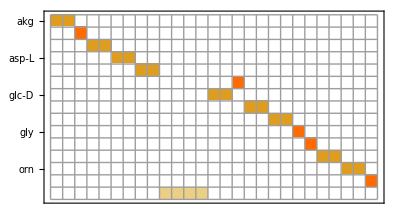

```mathematica
MatrixPlot[emuMixing,
FrameTicks->{Transpose[{Range[Length[measuredMetNames]],measuredMetNames}],None},Mesh->True]
```

MIDs to fit
Select MID data by metabolite and sample group

```mathematica
midsToFit=Block[{sampleGroups,groupToIndex,metIndex},
sampleGroups=DeleteDuplicates[measuredMapUnique⟦All,2⟧];
groupToIndex=Table[Rule[g,Flatten[Position[sampleInfo,{g,_,"13C",_,Except[1],_}]]],{g,sampleGroups}];
metIndex=ReindexList[measuredMapUnique⟦All,1⟧,measuredMetIds];
Table[
Normal/@MIDNormalize/@measuredMIDs⟦metIndex⟦i⟧,Replace[measuredMapUnique⟦i,2⟧,groupToIndex]⟧,
{i,Length[measuredMapUnique]}]]
```

{{{0.299744,0.0513757,0.0437293,0.119975,0.,0.485176},{0.362012,0.0281665,0.0289986,0.0263182,0.,0.554505}},{{0.426365,0.0303387,0.0169872,0.526309},{0.261822,0.0287143,0.031535,0.677928}},{{0.833451,0.0417243,0.0005467,0.,0.,0.0446412,0.079637},{0.694793,0.0410656,0.000688342,0.,0.,0.0840333,0.17942}},{{0.40428,0.175604,0.046262,0.0425329,0.33132},{0.309063,0.145866,0.149066,0.0544715,0.341533}},{{0.243256,0.0143625,0.0145777,0.,0.0210066,0.696461,0.0103373},{0.210457,0.0102209,0.0172921,0.,0.0199504,0.728011,0.014068}},{{0.0909235,0.00622566,0.000718884,0.00154515,0.00119942,0.0472508,0.852137},{0.0882601,0.00614825,0.000437985,0.00132071,0.00113339,0.0505479,0.852152}},{{0.53597,0.0341928,0.00697775,0.00612444,0.,0.038904,0.377831},{0.449923,0.0211853,0.00443393,0.00262439,0.00570019,0.0429197,0.473213}},{{0.0499962,0.0118489,0.00863251,0.0137548,0.0270993,0.888668},{0.0438463,0.0112825,0.0092715,0.0142729,0.027447,0.89388}},{{0.253621,0.133997,0.0942981,0.184019,0.0156076,0.318458},{0.220144,0.119628,0.0969114,0.180953,0.0169768,0.365386}},{{0.339392,0.066849,0.593759},{0.29438,0.0541857,0.651434}},{{0.70255,0.046121,0.0294036,0.221926},{0.693754,0.0459181,0.0274331,0.232895}},{{0.320723,0.154381,0.168941,0.0490925,0.306863},{0.299387,0.150969,0.170762,0.0579583,0.320924}},{{0.301479,0.0147884,0.,0.000735914,0.0160101,0.666986},{0.240491,0.0110836,0.,0.00137912,0.0169542,0.730092}},{{0.695643,0.0468745,0.104237,0.153245},{0.540772,0.0636649,0.162791,0.232772}},{{0.858089,0.061936,0.0199226,0.0191892,0.0022919,0.00336176,0.0352093},{0.852275,0.0617381,0.0200743,0.0186839,0.00378743,0.00399841,0.0394427}}}

## Uptake/release data

### Concentration estimates from medium fold changes

This reflects net balance, not directional fluxes.

Fresh medium concentrations (M)

```mathematica
initConc=Rest[Import["C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\medium-concentrations\\williams_E.txt","TSV"]];
initConc=Cases[initConc,{Alternatives@@(MetaboliteID/@InputMetabolites[net]),_}];
{measuredBoundaryIds,initConc}=Transpose[initConc];
measuredBoundaryIds=Partition[measuredBoundaryIds,1];
```

Fold changes fresh (incubated) medium, paired

```mathematica
Extract[sampleIds,
Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]]
```

{H_MS_U_FM24h_1,H_MS_U_FM24h_2,H_MS_U_FM24h_3}

```mathematica
mediumFoldchange=Block[{metIndex,freshIndex,spentIndex,freshPa,spentPa},
metIndex=ReindexList[measuredBoundaryIds,measuredMetIds];
freshIndex=Flatten[Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]];
spentIndex=Flatten[Position[sampleInfo,{"spent medium 24h",_,"12C",_,Except[1],_}]];
freshPa=Map[Normal[#]⟦1⟧&,measuredMIDs⟦metIndex,freshIndex⟧,{2}];
spentPa=Map[Normal[#]⟦1⟧&,measuredMIDs⟦metIndex,spentIndex⟧,{2}];
spentPa/(Mean/@freshPa)];
```

```mathematica
TableForm[mediumFoldchange,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | 0.707058 | 0.649568 | 0.637019
{arg-L} | 0.649441 | 0.896945 | 1.26799
{asp-L} | 0.708741 | 0.619282 | 0.686753
{gln-L} | 0.775106 | 0.677992 | 0.691322
{gly} | 0.772581 | 0.668197 | 0.579593
{ser-L} | 0.717339 | 0.620893 | 0.566426
{glc-D} | 0.931016 | 0.842854 | 0.792857

Convert to concentration differences

```mathematica
mediumConcDiff=initConc*(mediumFoldchange-1);
```

In um

```mathematica
TableForm[mediumConcDiff*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -295.872 | -353.936 | -366.611
{arg-L} | -83.0826 | -24.4241 | 63.5144
{asp-L} | -65.8246 | -86.0422 | -70.7937
{gln-L} | -449.787 | -644.016 | -617.355
{gly} | -151.688 | -221.312 | -280.411
{ser-L} | -26.9093 | -36.091 | -41.2762
{glc-D} | -765.722 | -1744.32 | -2299.29

### As mean +/- std dev

```mathematica
mediumConcDiffMean=Mean/@mediumConcDiff;
```

```mathematica
mediumConcDiffSD=StandardDeviation/@mediumConcDiff;
```

```mathematica
TableForm[Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -338.806 | 37.7187
{arg-L} | -14.6641 | 73.7842
{asp-L} | -74.2202 | 10.5353
{gln-L} | -570.386 | 105.289
{gly} | -217.804 | 64.4332
{ser-L} | -34.7588 | 7.27549
{glc-D} | -1603.11 | 776.475

### Add concentrations from clinical chemistry

Add lactate estimate (rough)

```mathematica
AppendTo[measuredBoundaryIds,{"lac-L"}];
AppendTo[mediumConcDiffMean,Mean[{1.0,1.5}]*0.001];
AppendTo[mediumConcDiffSD,StandardDeviation[{1.0,1.5}]*0.0001];
```

Add glucose total, for mixing

```mathematica
AppendTo[measuredBoundaryIds,{"glc-D_tot"}];
AppendTo[mediumConcDiffMean,initConc⟦7⟧];
AppendTo[mediumConcDiffSD,initConc⟦7⟧*0.001];
```

```mathematica
TableForm[Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -338.806 | 37.7187
{arg-L} | -14.6641 | 73.7842
{asp-L} | -74.2202 | 10.5353
{gln-L} | -570.386 | 105.289
{gly} | -217.804 | 64.4332
{ser-L} | -34.7588 | 7.27549
{glc-D} | -1603.11 | 776.475
{lac-L} | 1250. | 35.3553
{glc-D_tot} | 11100. | 11.1

### Calculate net uptake/release fluxes

Convert to fluxes (positive = release)

```mathematica
mediumVolume=0.0013;
cultureTime=24;
```

In nmol / h

```mathematica
TableForm[
Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*mediumVolume/cultureTime*10^9,
TableHeadings->{measuredBoundaryIds,{"mean","stddev"}}]
```

| mean | stddev
{ala-L} | -18.352 | 2.04309
{arg-L} | -0.794304 | 3.99665
{asp-L} | -4.02026 | 0.570664
{gln-L} | -30.8959 | 5.70315
{gly} | -11.7977 | 3.49013
{ser-L} | -1.88277 | 0.394089
{glc-D} | -86.8352 | 42.0591
{lac-L} | 67.7083 | 1.91508
{glc-D_tot} | 601.25 | 0.60125

### Map uptake/release measurements to EMU fluxes (flux mixing matrix)

Edit this to map to define measured reactions (linear combinations)

```mathematica
fluxMeasurementMap={
{"ala-L","ala-L_IN",-1},{"ala-L","ala-L_OUT",1},
{"arg-L","arg-L_IN",-1},{"arg-L","arg-L_OUT",1},
{"asp-L","asp-L_IN",-1},{"asp-L","asp-L_OUT",1},
{"gln-L","gln-L_IN",-1},
{"gly","gly_IN",-1},
{"ser-L","ser-L_IN",-1},{"ser-L","ser-L_OUT",1},
{"lac-L","lac-L_OUT",1},
{"glc-D","GLCtin_f",1},
{"glc-D_tot","GLCmix_f",1}
};
```

```mathematica
measFluxNames=ListToString/@measuredBoundaryIds
```

{ala-L,arg-L,asp-L,gln-L,gly,ser-L,glc-D,lac-L,glc-D_tot}

```mathematica
measReactions=Union[fluxMeasurementMap⟦All,2⟧]
```

{ala-L_IN,ala-L_OUT,arg-L_IN,arg-L_OUT,asp-L_IN,asp-L_OUT,GLCmix_f,GLCtin_f,gln-L_IN,gly_IN,lac-L_OUT,ser-L_IN,ser-L_OUT}

```mathematica
fluxMixing=SparseArray[
Thread[Rule[
Transpose[{
ReindexList[fluxMeasurementMap⟦All,1⟧,measFluxNames],
ReindexList[fluxMeasurementMap⟦All,2⟧,measReactions]}],
fluxMeasurementMap⟦All,3⟧]],
{Length[measFluxNames],Length[measReactions]}]
```

SparseArray[<13>, {9, 13}]

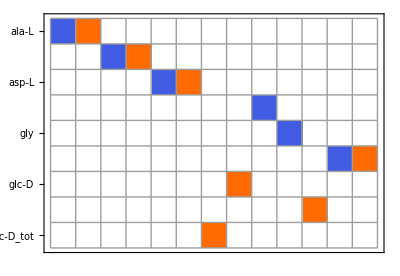

```mathematica
MatrixPlot[fluxMixing,
FrameTicks->{Transpose[{Range[Length[measFluxNames]],measFluxNames}],None},Mesh->True]
```

#### Schematic for fitting spent medium

-Graphics-

We would need to represent x_e and x_0 as separate metabolite pools, set glc-D_IN = glc-D_OUT = n_0/T and fit the difference v_2-v_1 to the uptake-release value. then v_3 = GLCmix is constrained by the MID balances, and v_1, v_2 become constrained by stoichiometry. For this we need linear combinations of fluxes in the objective.

## Characterize the flux space

### Min/max fluxes

Note that this works in the space of net fluxes and hence excludes type III pathways!
Reactions that cannot carry net flux may still be important to fit MIDs because of exchange fluxes.

It would probably be better to run this with the sink output fixed at a smaller value (100) to get numerically more well-behaved solutions

```mathematica
netFluxMinMax=FindViableReactions[net,Tolerance->10.^-6];
Dimensions[netFluxMinMax]
```

{89,2}

Convert to absolute flux states and remove duplicates

```mathematica
fluxMinMax=Union[Chop[Join[
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,1⟧}],
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,2⟧}]]]];
```

```mathematica
Length[fluxMinMax]
```

75

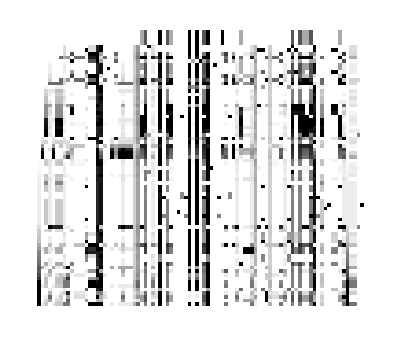

```mathematica
ArrayPlot[ForwardFlux/@fluxMinMax]
```

Generating random flux states from the min/max vectors, scaled to output = 100

```mathematica
RandomFluxState[n_]:=
Block[{f},
f=Mean[RandomChoice[fluxMinMax,n]]+0.001*Mean[fluxMinMax];
f/Total[PositivePart[MassBalance[net,f]]]*100]
```

### Check for blocked reactions

Reactions that cannot carry net flux in either direction.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,0}]//TableForm
```

<Reaction GHMT2r(rev)> | ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c | 0 | 0

Reactions that cannot carry net flux in the forward direction but in the reverse.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,_?Positive}]
```

{}

Reversible reactions that cannot carry net flux in the reverse direction.

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Intersection[
Position[Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001],0],
Position[ReversibleQ[Reactions[net]],True]]]}]//TableForm
```

<Reaction ACONTm(rev)> | cit_m <=> icit_m
<Reaction AKGDm(rev)> | akg_m + coa_m + nad_m <=> co2_m + nadh_m + succoa_m
<Reaction ASPTAm(rev)> | glu-L_m + oaa_m <=> akg_m + asp-L_m
<Reaction ATPtm(rev)> | adp_c + atp_m <=> adp_m + atp_c
<Reaction FBA(rev)> | fdp_c <=> dhap_c + g3p_c
<Reaction GHMT2r(rev)> | ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c
<Reaction GLUNm(rev)> | gln-L_m + h2o_m <=> glu-L_m + nh4_m
<Reaction ICDHxm(rev)> | icit_m + nad_m <=> akg_m + co2_m + nadh_m
<Reaction LDH_L(rev)> | h_c + nadh_c + pyr_c <=> lac-L_c + nad_c
<Reaction MDHm(rev)> | mal-L_m + nad_m <=> h_m + nadh_m + oaa_m
<Reaction PGI(rev)> | g6p_c <=> f6p_c
<Reaction PYRt2m(rev)> | pyr_c <=> pyr_m

Boundary fluxes that are never non-zero.

```mathematica
Pick[InputMetabolites[net],Chop[Max/@Transpose[BoundaryUptake/@fluxMinMax],.01],0]
```

{Metabolite[arg-L,Input,Boundary],Metabolite[glyc,Input,Boundary]}

```mathematica
Pick[OutputMetabolites[net],Chop[Max/@Transpose[BoundaryRelease/@fluxMinMax],0.01],0]
```

{}

## EMU model

### EMU decomposition

Find EMU reactions (this takes some time)

```mathematica
emuReactions=EMUAlgorithm[net,atomMaps,bmaps,{"C"},targets,symmetry];
Length[emuReactions]
```

911

```mathematica
emuReactionNames=EMUFluxMap[net,"reactions"];
```

```mathematica
RandomSample[emuReactions,10]
```

{EMUReaction[122,<glu-L_m{(1234)}>,<glu-L_c{(1234)}>,1],EMUReaction[33,<glu-L_m{(24)}>,<akg_m{(24)}>,1],EMUReaction[121,<glu-L_m{(12)}>,<gln-L_m{(12)}>,1],EMUReaction[85,<hco3_m{(1)}>,<oaa_m{(3)}>,1],EMUReaction[19,<2amac_c{(123)}>,<pyr_c{(123)}>,1],EMUReaction[23,<acrn_c{(12)}>,<acrn_m{(12)}>,1],EMUReaction[92,<3pg_c{(1)}>,<2pg_c{(1)}>,1],EMUReaction[19,<2amac_c{(12)}>,<pyr_c{(12)}>,1],EMUReaction[55,<g3p_c{(3)}>,<13dpg_c{(2)}>,1],EMUReaction[125,<akg_m{(35)}>,<icit_m{(13)}>,1]}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

458

```mathematica
SortBy[
Cases[emuReactions,
EMUReaction[i_,s_EMU,p:EMU[Metabolite["glc-D",__],_],_]:>{emuReactionNames⟦i⟧,s,p}],Last]//TableForm
```

GLCtin_f | <glc-D_v{(1)}> | <glc-D_c{(1)}>
GLCtin_f | <glc-D_v{(2)}> | <glc-D_c{(2)}>
GLCtin_f | <glc-D_v{(3)}> | <glc-D_c{(3)}>
GLCtin_f | <glc-D_v{(4)}> | <glc-D_c{(4)}>
GLCtin_f | <glc-D_v{(5)}> | <glc-D_c{(5)}>
GLCtin_f | <glc-D_v{(6)}> | <glc-D_c{(6)}>
GLCtin_f | <glc-D_v{(12)}> | <glc-D_c{(12)}>
GLCtin_f | <glc-D_v{(23)}> | <glc-D_c{(23)}>
GLCtin_f | <glc-D_v{(45)}> | <glc-D_c{(45)}>
GLCtin_f | <glc-D_v{(56)}> | <glc-D_c{(56)}>
GLCtin_f | <glc-D_v{(123)}> | <glc-D_c{(123)}>
GLCtin_f | <glc-D_v{(456)}> | <glc-D_c{(456)}>
GLCtin_f | <glc-D_v{(123456)}> | <glc-D_c{(123456)}>
G6PPer_f | <g6p_r{(123456)}> | <glc-D_r{(123456)}>
GLCmix_f | <glc-D_v{(123456)}> | <glc-D_e{(123456)}>
GLCtout_f | <glc-D_r{(123456)}> | <glc-D_e{(123456)}>
glc-D_IN | <glc-D_i{(1)}> | <glc-D_v{(1)}>
glc-D_IN | <glc-D_i{(2)}> | <glc-D_v{(2)}>
glc-D_IN | <glc-D_i{(3)}> | <glc-D_v{(3)}>
glc-D_IN | <glc-D_i{(4)}> | <glc-D_v{(4)}>
glc-D_IN | <glc-D_i{(5)}> | <glc-D_v{(5)}>
glc-D_IN | <glc-D_i{(6)}> | <glc-D_v{(6)}>
glc-D_IN | <glc-D_i{(12)}> | <glc-D_v{(12)}>
glc-D_IN | <glc-D_i{(23)}> | <glc-D_v{(23)}>
glc-D_IN | <glc-D_i{(45)}> | <glc-D_v{(45)}>
glc-D_IN | <glc-D_i{(56)}> | <glc-D_v{(56)}>
glc-D_IN | <glc-D_i{(123)}> | <glc-D_v{(123)}>
glc-D_IN | <glc-D_i{(456)}> | <glc-D_v{(456)}>
glc-D_IN | <glc-D_i{(123456)}> | <glc-D_v{(123456)}>

Ensure targets are contained in EMUs

```mathematica
Complement[targets,emus]
```

{}

### Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 196 internals, 35 substrates, 0 condensations >
2 | <EMUEquation (2), 136 internals, 23 substrates, 5 condensations >
3 | <EMUEquation (3), 72 internals, 12 substrates, 4 condensations >
4 | <EMUEquation (4), 22 internals, 2 substrates, 3 condensations >
5 | <EMUEquation (5), 16 internals, 3 substrates, 2 condensations >
6 | <EMUEquation (6), 16 internals, 4 substrates, 2 condensations >

## Substrates

### Check substrate purity against fresh medium MIDs

```mathematica
freshMediumMIDs=Block[{metIndex,freshIndex},
metIndex=ReindexList[measuredBoundaryIds,measuredMetIds];
freshIndex=Flatten[Position[sampleInfo,{"fresh medium 24h",_,"13C",_,Except[1],_}]];
Replace[metIndex,{i_Integer:>Normal/@MIDNormalize/@measuredMIDs⟦i,freshIndex⟧},1]];
```

```mathematica
TableForm[Mean/@freshMediumMIDs,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | 0.00334087 | 0.000318284 | 0.014643 | 0.981698 |  |  | 
{arg-L} | 0.00128799 | 0.0000125828 | 0. | 0. | 0.000566733 | 0.0386296 | 0.959503
{asp-L} | 0.000661918 | 0. | 0.000258311 | 0.0294335 | 0.969646 |  | 
{gln-L} | 0.000059953 | 0.000035674 | 0.0000889447 | 0.000448628 | 0.0293009 | 0.970066 | 
{gly} | 0.0166696 | 0.00601337 | 0.977317 |  |  |  | 
{ser-L} | 0. | 0. | 0.0249283 | 0.975072 |  |  | 
{glc-D} | 0.00283041 | 0. | 0. | 0. | 0.000707877 | 0.0548791 | 0.941583
{lac-L} | Mean[Missing] |  |  |  |  |  | 
{glc-D_tot} | Mean[Missing] |  |  |  |  |  |

Estimates tracer 13C enrichment from measured M+n fraction, as x_n^(1/n)

```mathematica
(Mean/@freshMediumMIDs)/.{x_?VectorQ:>Power[Last[x],1/(Length[x]-1)]}
```

{0.993862,0.993134,0.992324,0.99394,0.988593,0.991621,0.990018,Mean[Missing],Mean[Missing]}

### Specify input isotopomers (tracers)

Calculate MIDs for network substrate EMUs

```mathematica
irList=Table[
Rule[e,Total[Table[
PDF[MarginalizeToMID[
FragmentIsotopomerDistribution[
MetaboliteShortName[Metabolite[e]]/.substrateDist,a]],
x],
{a,AtomNumbers[e]},{x,Tuples[Map[Range[0,Length[#]]&,a]]}]]],
{e,Flatten[SubstrateEMUs/@emuEq]}];
```

### Check: simulate steady-state mass isotopomer data

```mathematica
emuSol=EMUSimulate[emuEq,irList,EMUFluxMap[net][RandomFluxState[10]]]
```

<EMUSolution, 6 subsystems>

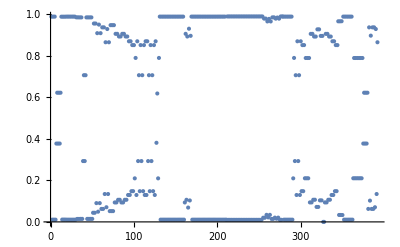
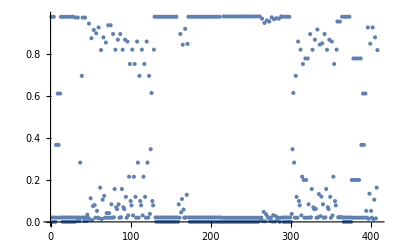
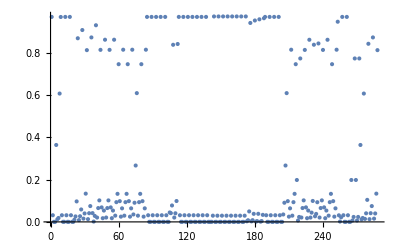
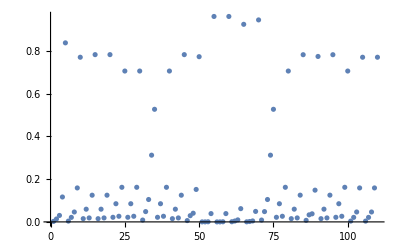
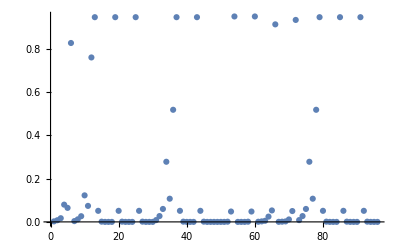
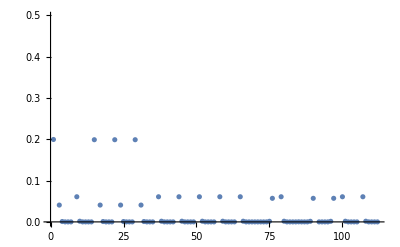

```mathematica
Table[
ListPlot[Flatten[InternalMIDs[emuSol,k]]],
{k,Length[emuEq]}]
```

```mathematica
Remove[emuSol]
```

## Analyze fluxes with GAMS, standard method

### Parameters

```mathematica
gamsModelName="liver-model";
```

```mathematica
gamsDir=FileNameJoin[{Directory[],"gams"}]
```

C:\code\liver-flux-analysis\flux-analysis-liver\gams

```mathematica
If[!DirectoryQ[gamsDir],CreateDirectory[gamsDir]]
```

Here “experiments” referes to tracer settings (only one)

```mathematica
experiments={"experiment1"};
```

Smallest standard deviation allowed

```mathematica
minSD=0.03;
```

```mathematica
Directory[]
```

C:\code\liver-flux-analysis\flux-analysis-liver

### Generate optimization model

Export model file

```mathematica
initFlux=RandomFluxState[10];
```

```mathematica
fluxCIReactions=Reactions[net];
```

```mathematica
fluxCIReactions=Cases[Reactions[net],Reaction["GLCtin"|"GLCmix"|"GLCtout"|"G6PPer"|"G6Pter"|"PGI",__]]
```

{<Reaction G6PPer>,<Reaction G6Pter>,<Reaction GLCmix>,<Reaction GLCtin>,<Reaction GLCtout>,<Reaction PGI(rev)>}

```mathematica
fluxCIReactions=Cases[Reactions[net],Reaction["GLCtout",__]]
```

{<Reaction GLCtout>}

```mathematica
GAMSExport[gamsDir,gamsModelName,
(* model *)
net,emuReactions,emuEq,{irList},
(* measured fluxes -- here we need to give a meas x reaction matrix *)
measFluxNames,measReactions,mediumConcDiffMean*mediumVolume/cultureTime*10^9,mediumConcDiffSD*mediumVolume/cultureTime*10^9,fluxMixing,
(* measured MIDs *)
experiments,measuredMetNames,{Mean/@midsToFit},{Map[Max[StandardDeviation[#],minSD]&,midsToFit]},
(* targets *)
targets,emuMixing,
initFlux,"FluxCI"->fluxCIReactions]
```

C:\code\liver-flux-analysis\flux-analysis-liver\gams\liver-model.gms

```mathematica
Length[Reactions[net]]
```

89

### Run GAMS

From command line ...

## Import GAMS solutions

### Estimated mixing matrix

```mathematica
emuMixingGams=ImportGAMSEmuMixing[gamsDir,gamsModelName,measuredMetNames,targets]
```

SparseArray[<25>, {15, 27}]

```mathematica
Block[{ij,mix},
ij=NonZeroIndices[emuMixingGams];
Transpose[{measuredMetNames⟦ij⟦All,1⟧⟧,targets⟦ij⟦All,2⟧⟧,NonZeroElements[emuMixingGams]}]]//TableForm
```

akg | <akg_c{(12345)}> | 1.
ala-L | <ala-L_c{(123)}> | 1.
arg-L | <arg-L_c{(123456)}> | 0.252724
arg-L | <arg-L_l{(123456)}> | 0.747276
asp-L | <asp-L_c{(1234)}> | 0.310891
asp-L | <asp-L_m{(1234)}> | 0.689109
citr-L | <citr-L_c{(123456)}> | 0.5
citr-L | <citr-L_m{(123456)}> | 0.5
glc-D_EC | <glc-D_e{(123456)}> | 1.
glc-D | <glc-D_c{(123456)}> | 0.463667
glc-D | <glc-D_r{(123456)}> | 0.536333
gln-L | <gln-L_c{(12345)}> | 0.484106
gln-L | <gln-L_m{(12345)}> | 0.515894
glu-L | <glu-L_c{(12345)}> | 1.
gly | <gly_c{(12)}> | 1.
glyc3p | <glyc3p_c{(123)}> | 1.
mal-L | <mal-L_c{(1234)}> | 0.266976
mal-L | <mal-L_m{(1234)}> | 0.733024
orn | <orn_c{(12345)}> | 0.5
orn | <orn_m{(12345)}> | 0.5
ser-L | <ser-L_c{(123)}> | 1.
f6p__g1p__g6p | <f6p_c{(123456)}> | 0.198937
f6p__g1p__g6p | <g1p_r{(123456)}> | 0.25
f6p__g1p__g6p | <g6p_c{(123456)}> | 0.069858
f6p__g1p__g6p | <g6p_r{(123456)}> | 0.481205

### Simulated MIDs

For all EMUs in the model

```mathematica
midGams=ImportGAMSIsotopes[gamsDir,gamsModelName,experiments,emus];
```

Check dimensions

```mathematica
Length/@midGams⟦1⟧==(EMUSize/@emus)+1
```

True

Check specific MIDs

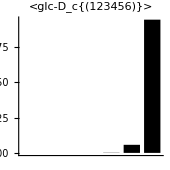
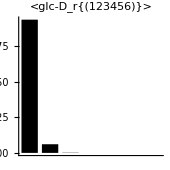
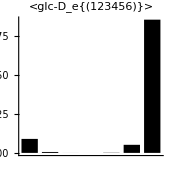
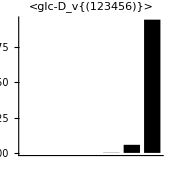

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["glc-D",_,_],{{{1,2,3,4,5,6}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

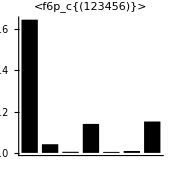
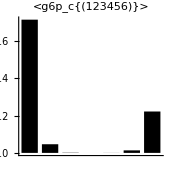
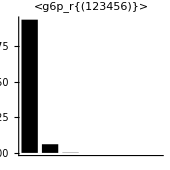

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["g6p"|"f6p",_,_],{{{1,2,3,4,5,6}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

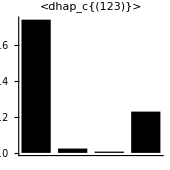
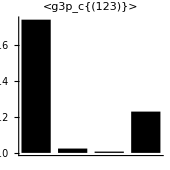
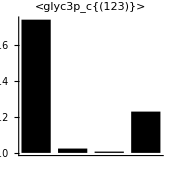

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["g3p"|"dhap"|"glyc3p",__],{{{1,2,3}}}]]];
Table[ 
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

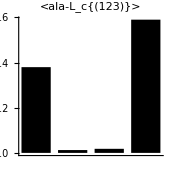
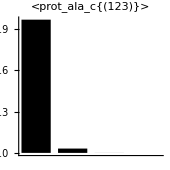
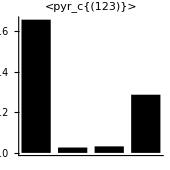
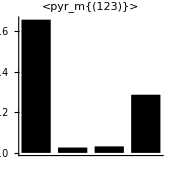

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["pyr"|"ala-L"|"prot_ala",_,_],{{{1,2,3}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

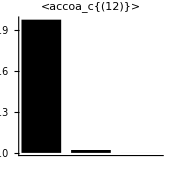
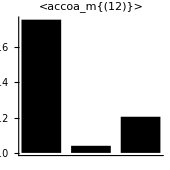

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["accoa",_,_],{{{1,2}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

### Fitted MIDs

Recover fitted MIDs as mixing x target MIDs

```mathematica
fittedMIDs=Block[{ix,mix,mid},
mix=emuMixingGams;
mid=midGams⟦1,ReindexList[targets,emus]⟧;
Table[
ix=Flatten[Position[em,_?Positive]];
em⟦ix⟧.mid⟦ix⟧,
{em,mix}]];
```

```mathematica
TableForm[fittedMIDs,TableHeadings->{measuredMetNames,None}]
```

akg | 0.248771 | 0.124175 | 0.141345 | 0.076405 | 0.0318922 | 0.377411 | 
ala-L | 0.379607 | 0.0124979 | 0.0180093 | 0.589886 |  |  | 
arg-L | 0.75973 | 0.0495986 | 0.00134969 | 0.000076068 | 0.00286099 | 0.0604603 | 0.125924
asp-L | 0.336613 | 0.0938258 | 0.104728 | 0.134774 | 0.330059 |  | 
citr-L | 0.231421 | 0.0189057 | 0.000623464 | 0.000717869 | 0.0350294 | 0.69416 | 0.0191427
glc-D_EC | 0.0893689 | 0.00579954 | 0.000156949 | 0.0000198175 | 0.00130356 | 0.0516201 | 0.851731
glc-D | 0.502809 | 0.0326295 | 0.000882347 | 0.0000217212 | 0.000668198 | 0.0264565 | 0.436533
gln-L | 0.0287454 | 0.0143484 | 0.016341 | 0.00968673 | 0.0461651 | 0.884713 | 
glu-L | 0.248771 | 0.124175 | 0.141345 | 0.076405 | 0.0318922 | 0.377411 | 
gly | 0.335306 | 0.0202696 | 0.644425 |  |  |  | 
glyc3p | 0.73952 | 0.0240655 | 0.00720522 | 0.229209 |  |  | 
mal-L | 0.29412 | 0.139575 | 0.162682 | 0.0975148 | 0.306108 |  | 
orn | 0.237811 | 0.0128606 | 0.000285533 | 0.000729808 | 0.0359766 | 0.712336 | 
ser-L | 0.57393 | 0.0465981 | 0.135855 | 0.243617 |  |  | 
f6p__g1p__g6p | 0.864036 | 0.0560796 | 0.00236225 | 0.0279631 | 0.000976257 | 0.00278538 | 0.0457971

Compare fitted MIDs (gray) with measured (black)

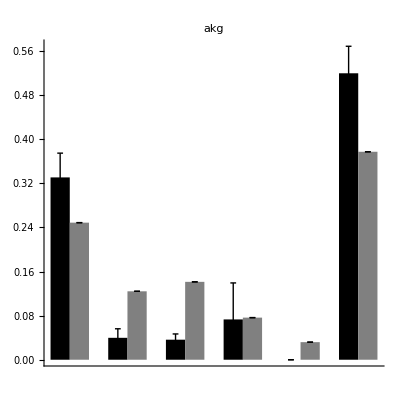
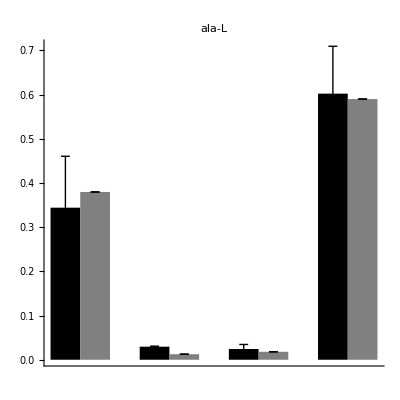
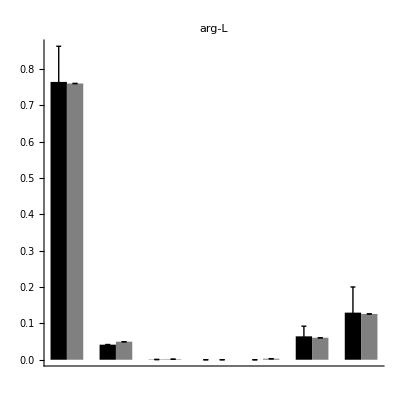
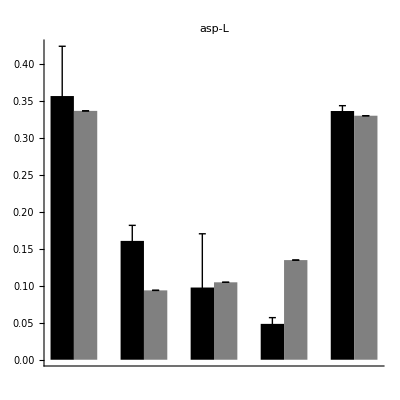
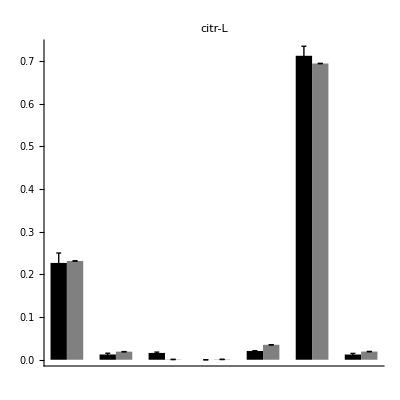
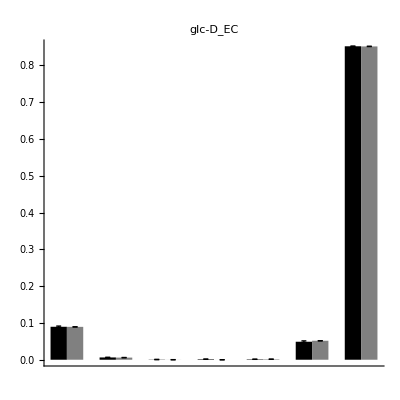
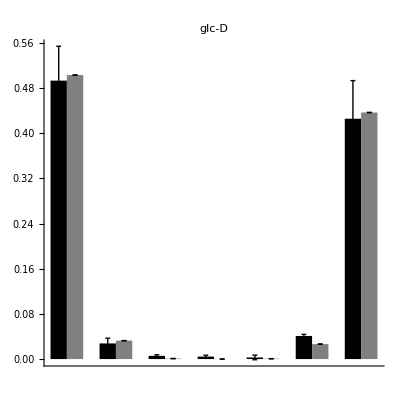
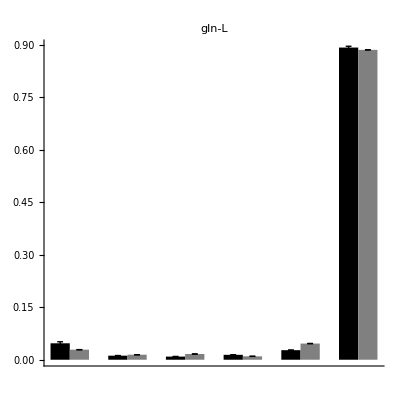

```mathematica
Table[
ErrorBarChart[
Transpose/@{midsToFit⟦i⟧,Table[fittedMIDs⟦i⟧,{3}]},
AspectRatio->1,PlotLabel->measuredMetNames⟦i⟧],
{i,Length[measuredMetNames]}]
```

Scatter plot of all fitted MIDs

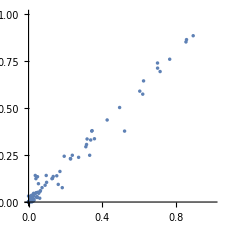

```mathematica
ListPlot[
Transpose[{Flatten[Mean/@midsToFit],Flatten[fittedMIDs]}],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

### Fluxes at optimum

```mathematica
fluxGams=ImportGAMSFluxes[gamsDir,gamsModelName,net,EMUFluxMap[net]]
```

<FluxState, 89 reactions, 33 b. exch>

```mathematica
TableForm[
Transpose[{ForwardFlux[fluxGams],ReverseFlux[fluxGams],NetFlux[fluxGams]}],
TableHeadings->{Reactions[net],{"fwd","rev","net"}}]
```

| fwd | rev | net
<Reaction 2AMACHYD> | 35.5523 | 0. | 35.5523
<Reaction ACITL> | 0.001 | 0. | 0.001
<Reaction ACOAHi> | 430.717 | 0. | 430.717
<Reaction ACONTm(rev)> | 120.176 | 0.001 | 120.175
<Reaction ACRNtm> | 35.0776 | 0. | 35.0776
<Reaction ACS> | 465.794 | 0. | 465.794
<Reaction ADK1> | 465.795 | 0. | 465.795
<Reaction AKGDm(rev)> | 10000. | 9928.14 | 71.856
<Reaction AKGtm(rev)> | 0.001 | 0.001 | 0.
<Reaction ALATA_L(rev)> | 29.7132 | 0.001 | 29.7122
<Reaction ARGN> | 0.00172114 | 0. | 0.00172114
<Reaction ARGSL> | 0.00172114 | 0. | 0.00172114
<Reaction ARGSS> | 0.00172114 | 0. | 0.00172114
<Reaction ASPTA(rev)> | 10000. | 9996. | 4.00013
<Reaction ASPTAm(rev)> | 0.002 | 0.001 | 0.001
<Reaction ASPtm> | 0.001 | 0. | 0.001
<Reaction ATPS4m> | 869.453 | 0. | 869.453
<Reaction ATPtm(rev)> | 896.988 | 0.001 | 896.987
<Reaction CBPSam> | 0.00172114 | 0. | 0.00172114
<Reaction CELLWORK> | 0.001 | 0. | 0.001
<Reaction CITtm> | 0.001 | 0. | 0.001
<Reaction CO2tm(rev)> | 9767.19 | 10000. | -232.809
<Reaction CRNtim> | 35.0776 | 0. | 35.0776
<Reaction CSm> | 120.176 | 0. | 120.176
<Reaction CSNATm> | 35.0776 | 0. | 35.0776
<Reaction CSNATr> | 35.0776 | 0. | 35.0776
<Reaction CYOOm> | 188.262 | 0. | 188.262
<Reaction CYOR-u10m> | 376.524 | 0. | 376.524
<Reaction ENO(rev)> | 131.885 | 0.001 | 131.884
<Reaction FBA(rev)> | 232.336 | 149.468 | 82.8686
<Reaction FBP> | 149.468 | 0. | 149.468
<Reaction FUMm> | 71.8578 | 0. | 71.8578
<Reaction FUMtm> | 0.00172114 | 0. | 0.00172114
<Reaction G3PD1> | 0.140373 | 0. | 0.140373
<Reaction G6PPer> | 63.3552 | 0. | 63.3552
<Reaction G6Pter> | 63.292 | 0. | 63.292
<Reaction GAPD(rev)> | 218.422 | 52.8256 | 165.597
<Reaction GHMT2r(rev)> | 13.5995 | 13.5995 | 0.
<Reaction GLCmix> | 601.25 | 0. | 601.25
<Reaction GLCtin> | 19.5765 | 0. | 19.5765
<Reaction GLCtout> | 63.3552 | 0. | 63.3552
<Reaction GLNtm> | 31.7391 | 0. | 31.7391
<Reaction GLUDxm(rev)> | 0.001 | 48.3213 | -48.3203
<Reaction GLUNm(rev)> | 40.8999 | 9.16081 | 31.7391
<Reaction GLUt2m(rev)> | 3.63356 | 83.692 | -80.0584
<Reaction GLYCOGEN_BREAK> | 126.647 | 0. | 126.647
<Reaction GLYCPH> | 0.141373 | 0. | 0.141373
<Reaction GLYK> | 0.001 | 0. | 0.001
<Reaction GTHS> | 10.9613 | 0. | 10.9613
<Reaction H2Oter> | 63.3552 | 0. | 63.3552
<Reaction H2Otm(rev)> | 0.001 | 1026.2 | -1026.2
<Reaction HCO3Em> | 44.3212 | 0. | 44.3212
<Reaction HEX1> | 19.5765 | 0. | 19.5765
<Reaction Htm2(rev)> | 4.57746 | 942.339 | -937.761
<Reaction ICDHxm(rev)> | 120.176 | 0.001 | 120.175
<Reaction LDH_L(rev)> | 67.7327 | 0.001 | 67.7317
<Reaction MALtm> | 4.00013 | 0. | 4.00013
<Reaction MDH> | 4.00013 | 0. | 4.00013
<Reaction MDHm(rev)> | 75.8589 | 0.001 | 75.8579
<Reaction NADH2-u10m> | 304.668 | 0. | 304.668
<Reaction NADH_REDOX(rev)> | 127.438 | 0.001 | 127.437
<Reaction NDPK1> | 0.001 | 0. | 0.001
<Reaction NH4tm(rev)> | 16.5839 | 0.001 | 16.5829
<Reaction O2tm> | 188.262 | 0. | 188.262
<Reaction OCBTm> | 0.00172114 | 0. | 0.00172114
<Reaction ORNt4m> | 0.00172114 | 0. | 0.00172114
<Reaction PCm> | 44.3194 | 0. | 44.3194
<Reaction PDHm> | 85.0988 | 0. | 85.0988
<Reaction PEPCK> | 0.001 | 0. | 0.001
<Reaction PFK> | 232.336 | 0. | 232.336
<Reaction PGCD> | 33.7124 | 0. | 33.7124
<Reaction PGI(rev)> | 82.8696 | 0.001 | 82.8686
<Reaction PGK(rev)> | 309.141 | 143.544 | 165.597
<Reaction PGM(rev)> | 131.885 | 0.001 | 131.884
<Reaction PGMTer> | 126.647 | 0. | 126.647
<Reaction PIt2m> | 896.987 | 0. | 896.987
<Reaction PIter> | 63.3552 | 0. | 63.3552
<Reaction PPA> | 465.795 | 0. | 465.795
<Reaction PROTDEG_ALA> | 11.649 | 0. | 11.649
<Reaction PROTDEG_ARG> | 0.001 | 0. | 0.001
<Reaction PSERT> | 33.7124 | 0. | 33.7124
<Reaction PSP_L> | 33.7124 | 0. | 33.7124
<Reaction PYK> | 131.885 | 0. | 131.885
<Reaction PYRt2m(rev)> | 129.419 | 0.001 | 129.418
<Reaction SERHL> | 35.5523 | 0. | 35.5523
<Reaction SUCD1m> | 71.856 | 0. | 71.856
<Reaction SUCOASm> | 71.856 | 0. | 71.856
<Reaction TPI(rev)> | 82.7292 | 0.001 | 82.7282
<Reaction ARG_tmL> | 0.001 | 0. | 0.001

Boundary fluxes

```mathematica
TableForm[
BoundaryFlux[fluxGams],
TableHeadings->{BoundaryFluxNames[bnet],None}]
```

ac_IN | 35.0766
ala-L_IN | 18.0642
arg-L_IN | 0.00298481
asp-L_IN | 10000.
co2_IN | 9767.19
glc-D_IN | 620.827
gln-L_IN | 31.7391
glucys_IN | 10.9613
gly_IN | 10.9613
glyc_IN | 0.001
glycogen_IN | 126.647
h2o_IN | 0.001
h_IN | 0.001
nh4_IN | 2.38498
o2_IN | 188.262
prot_ala_IN | 11.649
prot_arg_IN | 0.001
ser-L_IN | 1.84092
ala-L_OUT | 0.001
arg-L_OUT | 0.00398481
asp-L_OUT | 9996.
co2_OUT | 10000.
energy_OUT | 0.001
glc-D_OUT | 664.605
glu-L_OUT | 80.0584
glyc_OUT | 0.141373
gthrd_OUT | 10.9613
h2o_OUT | 14.8968
h_OUT | 344.618
lac-L_OUT | 67.7317
nh4_OUT | 21.3544
ser-L_OUT | 0.001
urea_OUT | 0.00172114

Fitted flux measurements. This now needs to combine internal and boundary fluxes ,,,

```mathematica
Block[{ix,rl,v},
rl=Join[EMUFluxMap[net,"reactions"],BoundaryFluxNames[bnet]];
v=Join[EMUFluxMap[net][fluxGams],BoundaryFlux[fluxGams]];
ix=ReindexList[measReactions,rl];
TableForm[
Transpose[{fluxMixing.v⟦ix⟧,mediumConcDiffMean*mediumVolume/cultureTime*10^9}],
TableHeadings->{measFluxNames,{"fitted","measured"}}]]
```

| fitted | measured
ala-L | -18.0632 | -18.352
arg-L | 0.001 | -0.794304
asp-L | -4.00085 | -4.02026
gln-L | -31.7391 | -30.8959
gly | -10.9613 | -11.7977
ser-L | -1.83992 | -1.88277
glc-D | 19.5765 | -86.8352
lac-L | 67.7317 | 67.7083
glc-D_tot | 601.25 | 601.25

### Check objective

GAMS objective =  70.79, range objecive <= 70.29 +  2.70 = 73.49

```mathematica
70.79+2.7
```

73.49

```mathematica
Map[Max[StandardDeviation[#],minSD]&,midsToFit]
```

{0.0662253,0.116349,0.0980459,0.0726937,0.03,0.03,0.0674452,0.03,0.0331833,0.0407826,0.03,0.03,0.0446224,0.10951,0.03}

Residuals for each fitted MID and

```mathematica
midChi=(fittedMIDs-Mean/@midsToFit)/Map[Max[StandardDeviation[#],minSD]&,midsToFit];
TableForm[midChi,TableHeadings->{measuredMetNames,None}]
```

akg | -1.23981 | 1.2745 | 1.5852 | 0.0492014 | 0.481571 | -2.15067 | 
ala-L | 0.30523 | -0.146358 | -0.0537327 | -0.105139 |  |  | 
arg-L | -0.0447923 | 0.0836715 | 0.00746761 | 0.000775841 | 0.0291801 | -0.0395422 | -0.0367605
asp-L | -0.275928 | -0.920429 | 0.0971715 | 1.18678 | -0.0875957 |  | 
citr-L | 0.152139 | 0.220467 | -0.51038 | 0.023929 | 0.48503 | -0.602522 | 0.231337
glc-D_EC | -0.00743182 | -0.0129139 | -0.0140495 | -0.0471037 | 0.00457173 | 0.0906901 | -0.013763
glc-D | 0.146226 | 0.0732508 | -0.0715172 | -0.0645368 | -0.0323507 | -0.214326 | 0.163254
gln-L | -0.605862 | 0.0927579 | 0.246298 | -0.144238 | 0.629732 | -0.218689 | 
glu-L | 0.358282 | -0.0794738 | 1.3784 | -3.19682 | 0.470116 | 1.0695 | 
gly | 0.451649 | -0.986884 | 0.535235 |  |  |  | 
glyc3p | 1.37895 | -0.731802 | -0.707106 | 0.0599587 |  |  | 
mal-L | -0.531194 | -0.436661 | -0.238962 | 1.46631 | -0.259497 |  | 
orn | -0.743435 | -0.00169113 | 0.00639887 | -0.00734405 | 0.436876 | 0.309196 | 
ser-L | -0.404327 | -0.079185 | 0.0213771 | 0.462134 |  |  | 
f6p__g1p__g6p | 0.295135 | -0.191913 | -0.587873 | 0.300885 | -0.0687803 | -0.0298237 | 0.28237

```mathematica
Flatten[midChi]//Length
```

84

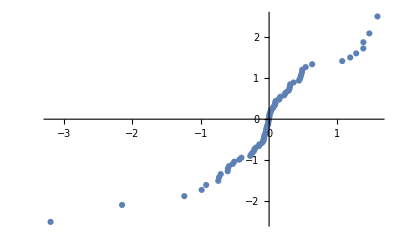

```mathematica
Block[{qObs,q0,labels,ix},
qObs=Flatten[midChi];
labels=Flatten[Table[measuredMetNames⟦i⟧,{i,Length[midChi]},{Length[midChi⟦i⟧]}]];
ix=Ordering[qObs];
q0=Quantile[NormalDistribution[0,1],N[(Range[Length[qObs]]-1/2)/Length[qObs]]];
ListPlot[
Thread[Tooltip[Transpose[{qObs⟦ix⟧,q0}],labels⟦ix⟧]],
PlotRange->All]]
```

Chi square = sum of squared residuals

```mathematica
TableForm[midChi^2,TableHeadings->{measuredMetNames,None}]
```

akg | 1.53712 | 1.62435 | 2.51287 | 0.00242078 | 0.231911 | 4.6254 | 
ala-L | 0.0931651 | 0.0214206 | 0.0028872 | 0.0110543 |  |  | 
arg-L | 0.00200635 | 0.00700092 | 0.0000557652 | 6.01929×10^-7 | 0.000851478 | 0.00156359 | 0.00135134
asp-L | 0.0761363 | 0.84719 | 0.0094423 | 1.40845 | 0.00767301 |  | 
citr-L | 0.0231463 | 0.0486055 | 0.260488 | 0.000572596 | 0.235254 | 0.363032 | 0.0535168
glc-D_EC | 0.0000552319 | 0.000166768 | 0.000197389 | 0.00221876 | 0.0000209007 | 0.0082247 | 0.000189419
glc-D | 0.0213821 | 0.00536568 | 0.00511471 | 0.004165 | 0.00104657 | 0.0459358 | 0.0266519
gln-L | 0.367069 | 0.00860403 | 0.0606629 | 0.0208045 | 0.396562 | 0.0478248 | 
glu-L | 0.128366 | 0.00631609 | 1.89999 | 10.2197 | 0.221009 | 1.14383 | 
gly | 0.203987 | 0.973941 | 0.286477 |  |  |  | 
glyc3p | 1.9015 | 0.535534 | 0.499999 | 0.00359505 |  |  | 
mal-L | 0.282167 | 0.190673 | 0.0571028 | 2.15008 | 0.0673385 |  | 
orn | 0.552696 | 2.85993×10^-6 | 0.0000409456 | 0.0000539351 | 0.19086 | 0.095602 | 
ser-L | 0.16348 | 0.00627026 | 0.000456982 | 0.213568 |  |  | 
f6p__g1p__g6p | 0.0871045 | 0.0368308 | 0.345594 | 0.0905317 | 0.00473073 | 0.000889452 | 0.0797331

```mathematica
Total[Flatten[midChi^2]]
```

37.6712

Flux errors

```mathematica
fluxChi=Block[{ix,rl,v},
rl=Join[EMUFluxMap[net,"reactions"],BoundaryFluxNames[bnet]];
v=Join[EMUFluxMap[net][fluxGams],BoundaryFlux[fluxGams]];
ix=ReindexList[measReactions,rl];
(fluxMixing.v⟦ix⟧-mediumConcDiffMean*mediumVolume/cultureTime*10^9)/(mediumConcDiffMean*mediumVolume/cultureTime*10^9)]
```

{-0.0157355,-1.00126,-0.00482768,0.0272921,-0.0708978,-0.0227571,-1.22544,0.000345591,0.}

```mathematica
Total[Flatten[{midChi^2,fluxChi^2}]]
```

40.182

### Flux confidence intervals

```mathematica
fluxCI=Block[{hi,low},
{hi,low}={
Import[FileNameJoin[{gamsDir, gamsModelName<>"_fluxhi.tsv"}], "TSV"],
Import[FileNameJoin[{gamsDir, gamsModelName<>"_fluxlow.tsv"}], "TSV"]};
(* ensure CI list matches the given list above *)
If[hi⟦All,1⟧==ReactionID/@fluxCIReactions,
Transpose[{low⟦All,2⟧,hi⟦All,2⟧}],
$Failed]];
```

```mathematica
TableForm[fluxCI,TableHeadings->{fluxCIReactions,{"min","max"}}]
```

| min | max
<Reaction 2AMACHYD> | 18.6312 | 57.6283
<Reaction ACITL> | 0.001 | 486.386
<Reaction ACOAHi> | 0.001 | 1667.06
<Reaction ACONTm(rev)> | 55.3235 | 328.418
<Reaction ACRNtm> | 2.44285 | 136.764
<Reaction ACS> | 2.44285 | 1786.95
<Reaction ADK1> | 2.44457 | 1786.95
<Reaction AKGDm(rev)> | 10.1149 | 282.658
<Reaction AKGtm(rev)> | -25.0879 | 13.9955
<Reaction ALATA_L(rev)> | 16.6555 | 52.6136
<Reaction ARGN> | 0.001 | 14.2581
<Reaction ARGSL> | 0.001 | 14.2581
<Reaction ARGSS> | 0.001 | 14.2581
<Reaction ASPTA(rev)> | -4.4696 | 12.224
<Reaction ASPTAm(rev)> | 0.001 | 8.21032
<Reaction ASPtm> | 0.001 | 8.21032
<Reaction ATPS4m> | 210.928 | 3057.46
<Reaction ATPtm(rev)> | 178.598 | 3296.53
<Reaction CBPSam> | 0.001 | 14.2581
<Reaction CELLWORK> | 0.001 | 3334.13
<Reaction CITtm> | 0.001 | 486.386
<Reaction CO2tm(rev)> | -771.921 | -67.3369
<Reaction CRNtim> | 2.44285 | 136.764
<Reaction CSm> | 55.3245 | 328.419
<Reaction CSNATm> | 2.44285 | 136.764
<Reaction CSNATr> | 2.44285 | 136.764
<Reaction CYOOm> | 44.2707 | 667.941
<Reaction CYOR-u10m> | 88.5413 | 1335.88
<Reaction ENO(rev)> | 70.1831 | 262.456
<Reaction FBA(rev)> | 54.6848 | 174.744
<Reaction FBP> | 0.001 | 3396.08
<Reaction FUMm> | 10.1166 | 282.66
<Reaction FUMtm> | 0.001 | 14.2581
<Reaction G3PD1> | 0.00205533 | 175.207
<Reaction G6PPer> | 37.1962 | 91.7497
<Reaction G6Pter> | 41.6734 | 134.04
<Reaction GAPD(rev)> | 109.284 | 295.661
<Reaction GHMT2r(rev)> | 0. | 0.
<Reaction GLCmix> | 600.261 | 602.239
<Reaction GLCtin> | 12.602 | 41.2205
<Reaction GLCtout> | 37.1962 | 91.7497
<Reaction GLNtm> | 23.3489 | 40.4342
<Reaction GLUDxm(rev)> | -65.4423 | -21.7467
<Reaction GLUNm(rev)> | 23.3489 | 40.4342
<Reaction GLUt2m(rev)> | -104.286 | -50.3212
<Reaction GLYCOGEN_BREAK> | 90.977 | 200.426
<Reaction GLYCPH> | 0.00305533 | 3313.74
<Reaction GLYK> | 0.001 | 3312.75
<Reaction GTHS> | 5.80978 | 16.1785
<Reaction H2Oter> | 37.1962 | 91.7497
<Reaction H2Otm(rev)> | -3754.88 | -205.185
<Reaction HCO3Em> | 31.6453 | 63.8785
<Reaction HEX1> | 12.602 | 41.2205
<Reaction Htm2(rev)> | -3458.08 | -178.803
<Reaction ICDHxm(rev)> | 55.3235 | 328.418
<Reaction LDH_L(rev)> | 64.5828 | 70.8807
<Reaction MALtm> | 0.001 | 22.9155
<Reaction MDH> | 0.001 | 22.9155
<Reaction MDHm(rev)> | 14.1227 | 285.012
<Reaction NADH2-u10m> | 78.0671 | 1053.71
<Reaction NADH_REDOX(rev)> | -57.8035 | 257.864
<Reaction NDPK1> | 0.001 | 38.1183
<Reaction NH4tm(rev)> | -8.86548 | 31.761
<Reaction O2tm> | 44.2707 | 667.941
<Reaction OCBTm> | 0.001 | 14.2581
<Reaction ORNt4m> | 0.001 | 14.2581
<Reaction PCm> | 31.6436 | 62.3064
<Reaction PDHm> | 37.5407 | 214.707
<Reaction PEPCK> | 0.001 | 38.1183
<Reaction PFK> | 60.9108 | 3538.59
<Reaction PGCD> | 16.8633 | 55.7677
<Reaction PGI(rev)> | 54.6848 | 174.744
<Reaction PGK(rev)> | 109.284 | 295.661
<Reaction PGM(rev)> | 70.1831 | 262.456
<Reaction PGMTer> | 90.977 | 200.426
<Reaction PIt2m> | 178.598 | 3296.53
<Reaction PIter> | 37.1962 | 91.7497
<Reaction PPA> | 2.44457 | 1786.95
<Reaction PROTDEG_ALA> | 0.001 | 34.3795
<Reaction PROTDEG_ARG> | 0.001 | 5.44552
<Reaction PSERT> | 16.8633 | 55.7677
<Reaction PSP_L> | 16.8633 | 55.7677
<Reaction PYK> | 70.1841 | 262.9
<Reaction PYRt2m(rev)> | 74.3689 | 259.825
<Reaction SERHL> | 18.6312 | 57.6283
<Reaction SUCD1m> | 10.1149 | 282.658
<Reaction SUCOASm> | 10.1149 | 282.658
<Reaction TPI(rev)> | -9.95794 | 147.775
<Reaction ARG_tmL> | 0.001 | 5.44552

### TEMP: fluxes at CI max

#### Import flux vector

```mathematica
fluxGams=ImportGAMSFluxes["gams\\fluxes_max_GLCout.tsv",net,EMUFluxMap[net]]
```

<FluxState, 89 reactions, 33 b. exch>

```mathematica
TableForm[
Transpose[{ForwardFlux[fluxGams],ReverseFlux[fluxGams],NetFlux[fluxGams]}],
TableHeadings->{Reactions[net],{"fwd","rev","net"}}]
```

| fwd | rev | net
<Reaction 2AMACHYD> | 74.0512 | 0. | 74.0512
<Reaction ACITL> | 1.98708 | 0. | 1.98708
<Reaction ACOAHi> | 752.986 | 0. | 752.986
<Reaction ACONTm(rev)> | 271.664 | 0.001 | 271.663
<Reaction ACRNtm> | 273.649 | 0. | 273.649
<Reaction ACS> | 1024.65 | 0. | 1024.65
<Reaction ADK1> | 1024.65 | 0. | 1024.65
<Reaction AKGDm(rev)> | 10000. | 9786.76 | 213.239
<Reaction AKGtm(rev)> | 23.5591 | 0.001 | 23.5581
<Reaction ALATA_L(rev)> | 44.5116 | 0.001 | 44.5106
<Reaction ARGN> | 0.00219546 | 0. | 0.00219546
<Reaction ARGSL> | 0.00219546 | 0. | 0.00219546
<Reaction ARGSS> | 0.00219546 | 0. | 0.00219546
<Reaction ASPTA(rev)> | 10000. | 9995.9 | 4.0998
<Reaction ASPTAm(rev)> | 0.0827361 | 0.001 | 0.0817361
<Reaction ASPtm> | 0.0817361 | 0. | 0.0817361
<Reaction ATPS4m> | 1866.67 | 0. | 1866.67
<Reaction ATPtm(rev)> | 2022.06 | 0.001 | 2022.05
<Reaction CBPSam> | 0.00219546 | 0. | 0.00219546
<Reaction CELLWORK> | 0.001 | 0. | 0.001
<Reaction CITtm> | 1.98708 | 0. | 1.98708
<Reaction CO2tm(rev)> | 0.001 | 427.055 | -427.054
<Reaction CRNtim> | 273.649 | 0. | 273.649
<Reaction CSm> | 273.65 | 0. | 273.65
<Reaction CSNATm> | 273.649 | 0. | 273.649
<Reaction CSNATr> | 273.649 | 0. | 273.649
<Reaction CYOOm> | 415.981 | 0. | 415.981
<Reaction CYOR-u10m> | 831.962 | 0. | 831.962
<Reaction ENO(rev)> | 3.55248 | 0.001 | 3.55148
<Reaction FBA(rev)> | 38.2376 | 0.001 | 38.2366
<Reaction FBP> | 0.001 | 0. | 0.001
<Reaction FUMm> | 213.241 | 0. | 213.241
<Reaction FUMtm> | 0.00219546 | 0. | 0.00219546
<Reaction G3PD1> | 0.753221 | 0. | 0.753221
<Reaction G6PPer> | 9403.75 | 0. | 9403.75
<Reaction G6Pter> | 38.2356 | 0. | 38.2356
<Reaction GAPD(rev)> | 76.4279 | 0.707943 | 75.72
<Reaction GHMT2r(rev)> | 23.2406 | 23.2406 | 0.
<Reaction GLCmix> | 596.249 | 0. | 596.249
<Reaction GLCtin> | 0.001 | 0. | 0.001
<Reaction GLCtout> | 9403.75 | 0. | 9403.75
<Reaction GLNtm> | 30.8959 | 0. | 30.8959
<Reaction GLUDxm(rev)> | 0.001 | 82.0651 | -82.0641
<Reaction GLUNm(rev)> | 34.4902 | 3.59427 | 30.8959
<Reaction GLUt2m(rev)> | 0.001 | 112.879 | -112.878
<Reaction GLYCOGEN_BREAK> | 9441.99 | 0. | 9441.99
<Reaction GLYCPH> | 0.754221 | 0. | 0.754221
<Reaction GLYK> | 0.001 | 0. | 0.001
<Reaction GTHS> | 11.7977 | 0. | 11.7977
<Reaction H2Oter> | 9403.75 | 0. | 9403.75
<Reaction H2Otm(rev)> | 3.47366 | 2208.53 | -2205.06
<Reaction HCO3Em> | 57.8484 | 0. | 57.8484
<Reaction HEX1> | 0.001 | 0. | 0.001
<Reaction Htm2(rev)> | 0.00100707 | 1962.22 | -1962.22
<Reaction ICDHxm(rev)> | 271.664 | 0.001 | 271.663
<Reaction LDH_L(rev)> | 67.7093 | 0.001 | 67.7083
<Reaction MALtm> | 2.64463 | 0. | 2.64463
<Reaction MDH> | 2.64463 | 0. | 2.64463
<Reaction MDHm(rev)> | 215.886 | 0.001 | 215.885
<Reaction NADH2-u10m> | 618.724 | 0. | 618.724
<Reaction NADH_REDOX(rev)> | 77.627 | 0.844755 | 76.7823
<Reaction NDPK1> | 3.44225 | 0. | 3.44225
<Reaction NH4tm(rev)> | 51.1714 | 0.001 | 51.1704
<Reaction O2tm> | 415.981 | 0. | 415.981
<Reaction OCBTm> | 0.00219546 | 0. | 0.00219546
<Reaction ORNt4m> | 0.00219546 | 0. | 0.00219546
<Reaction PCm> | 57.8462 | 0. | 57.8462
<Reaction PDHm> | 0.001 | 0. | 0.001
<Reaction PEPCK> | 3.44225 | 0. | 3.44225
<Reaction PFK> | 38.2376 | 0. | 38.2376
<Reaction PGCD> | 72.1685 | 0. | 72.1685
<Reaction PGI(rev)> | 38.2376 | 0.001 | 38.2366
<Reaction PGK(rev)> | 76.4279 | 0.707943 | 75.72
<Reaction PGM(rev)> | 5.22282 | 1.67134 | 3.55148
<Reaction PGMTer> | 9441.99 | 0. | 9441.99
<Reaction PIt2m> | 2022.05 | 0. | 2022.05
<Reaction PIter> | 9403.75 | 0. | 9403.75
<Reaction PPA> | 1024.65 | 0. | 1024.65
<Reaction PROTDEG_ALA> | 26.1585 | 0. | 26.1585
<Reaction PROTDEG_ARG> | 0.001 | 0. | 0.001
<Reaction PSERT> | 72.1685 | 0. | 72.1685
<Reaction PSP_L> | 72.1685 | 0. | 72.1685
<Reaction PYK> | 6.99374 | 0. | 6.99374
<Reaction PYRt2m(rev)> | 57.8482 | 0.001 | 57.8472
<Reaction SERHL> | 74.0512 | 0. | 74.0512
<Reaction SUCD1m> | 213.239 | 0. | 213.239
<Reaction SUCOASm> | 213.239 | 0. | 213.239
<Reaction TPI(rev)> | 37.4844 | 0.001 | 37.4834
<Reaction ARG_tmL> | 0.001 | 0. | 0.001

```mathematica
Cases[
Transpose[{Metabolites[net],Chop[MassBalance[net,fluxGams],10^-6]}],
{_,Except[0]}]//TableForm
```

Metabolite[ac,Cytosol,Uptake] | -271.662
Metabolite[ala-L,Cytosol,Free] | -18.352
Metabolite[arg-L,Cytosol,Free] | 0.001
Metabolite[asp-L,Cytosol,Free] | -4.02026
Metabolite[co2,Cytosol,Free] | 430.496
Metabolite[energy,Cytosol,Release] | 0.001
Metabolite[glc-D,Extracellular,Release] | 10000.
Metabolite[glc-D,Virtual,Uptake] | -596.25
Metabolite[gln-L,Cytosol,Uptake] | -30.8959
Metabolite[glucys,Cytosol,Uptake] | -11.7977
Metabolite[glu-L,Cytosol,Release] | 89.3201
Metabolite[gly,Cytosol,Uptake] | -11.7977
Metabolite[glyc,Cytosol,Free] | 0.753221
Metabolite[glycogen,EndoplasmicReticulum,Uptake] | -9441.99
Metabolite[gthrd,Cytosol,Release] | 11.7977
Metabolite[h2o,Cytosol,Free] | -9045.71
Metabolite[h,Cytosol,Free] | 12.0301
Metabolite[lac-L,Cytosol,Release] | 67.7083
Metabolite[nh4,Cytosol,Free] | 22.8809
Metabolite[o2,Cytosol,Uptake] | -415.981
Metabolite[prot_ala,Cytosol,Uptake] | -26.1585
Metabolite[prot_arg,Lysosome,Uptake] | -0.001
Metabolite[ser-L,Cytosol,Free] | -1.88277
Metabolite[urea,Cytosol,Release] | 0.00219546

#### Simulate MIDs

```mathematica
emuSol=EMUSimulate[emuEq,irList,EMUFluxMap[net][fluxGams]]
```

<EMUSolution, 6 subsystems>

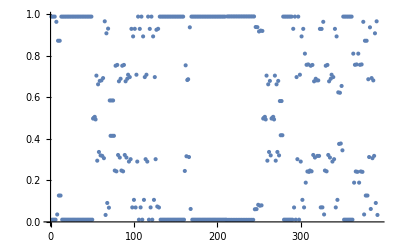
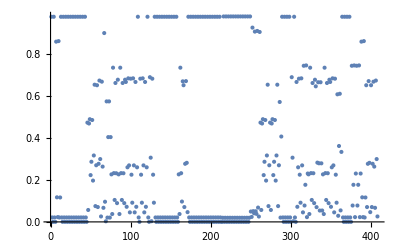
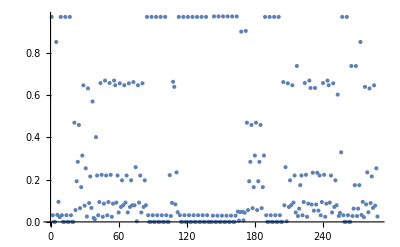
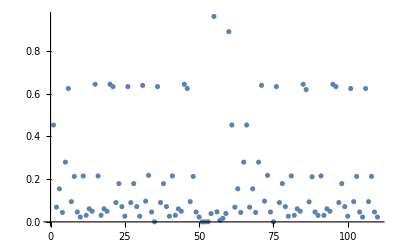
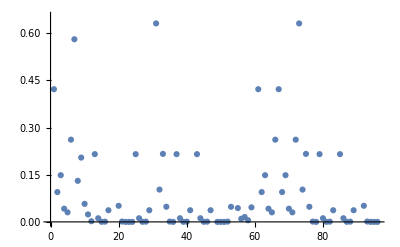
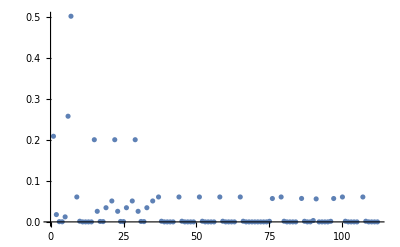

```mathematica
Table[
ListPlot[Flatten[InternalMIDs[emuSol,k]]],
{k,Length[emuEq]}]
```

```mathematica
emusToCheck=Cases[emus,EMU[Metabolite["glc-D",__],{{{1,2,3,4,5,6}}}]]
```

{<glc-D_c{(123456)}>,<glc-D_r{(123456)}>,<glc-D_e{(123456)}>,<glc-D_v{(123456)}>}

```mathematica
TableForm[
emuSol/@emusToCheck,
TableHeadings->{emusToCheck,None}]
```

<glc-D_c{(123456)}> | 1.×10^-12 | 5.94×10^-10 | 1.47015×10^-7 | 0.000019406 | 0.00144089 | 0.0570594 | 0.94148
<glc-D_r{(123456)}> | 0.937493 | 0.060838 | 0.00164502 | 0.0000237228 | 1.92434×10^-7 | 8.32527×10^-10 | 1.50073×10^-12
<glc-D_e{(123456)}> | 0.881595 | 0.0572106 | 0.00154694 | 0.0000234654 | 0.0000860941 | 0.00340216 | 0.0561356
<glc-D_v{(123456)}> | 1.×10^-12 | 5.94×10^-10 | 1.47015×10^-7 | 0.000019406 | 0.00144089 | 0.0570594 | 0.94148